BDW Hamiltonian
Definition of the hamiltonian elements and plot of the free electron dispersion relation

```mathematica
ClearAll["Global`*"]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

C:\Users\fywen\Downloads

```mathematica
$HistoryLength=0;
```

```mathematica
c=13.2;
a =5.3/Sqrt[2];
b=5.3/Sqrt[2];
ℏ=1.05*10^-34;
e=1.6*10^-19;
m0=9.1*10^-31;
kB=1.38*10^-23;
jtoev=6.242*10^18;
tdevs=10;
numb = 500;
gridnum=56;
cdev =8;
θmax=100;
θmin=0;
θdevs=8;

tnum=8;
tau = 0.08;


thetas = Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}]
phis = {0.*Pi/180,15.*Pi/180,30.*Pi/180,45.*Pi/180}

v [f_]:=(9.1*10^-31)10^-20/(10^-12)*1/ℏ{D[f,kx],D[f,ky],D[f,kz]};
kf[F_]:=Sqrt[(F 2Pi (e/(1.6*10^-19))/(ℏ/(9.1*10^-31)*10^20) (1/10^-12))/Pi];
ty= 1.6*10^-22 * 1/(9.1*10^-31) 1/(10^-10)^2 10^-24;
ftotal=(1.05*10^-34)(2Pi/(a*10^-10))^2 / (2 Pi *1.6*10^-19);
```

{0.,0.218166,0.436332,0.654498,0.872665,1.09083,1.309,1.52716,1.74533}

{0.,0.261799,0.523599,0.785398}

```mathematica
t=190*ty;
tp=-0.16*t;
tpp=0.07*t;
tz=0.035*t;
μ = 0.685*t;
ξ[kx_?NumericQ,ky_?NumericQ,mu_?NumericQ]:=-2t(Cos[kx a]+Cos[ky b])-2tp(Cos[kx a+ky b]+Cos[kx a- ky b])-2tpp(Cos[2kx a]+Cos[2ky b])+mu;
ξz[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];


Q=2π/3/a;
(*here it could be functions of kx and ky like for dwave density waves*)
B=0(*-0.07*t*);
AA=0.1*t;

(*here it could be functions of kx and ky like for dwave density waves*)
tyQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);
txQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b] );
tsyQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);
tsxQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);

BDW2d[kx_,ky_,mu_]=({{ξ[kx,ky,mu], -tyQ[kx,ky+Q/2], -tyQ[kx,ky-Q/2], -txQ[kx+Q/2,ky], 0, 0, -txQ[kx-Q/2,ky], 0, 0}, {-tyQ[kx,ky+Q/2], ξ[kx,ky+Q,mu], -tyQ[kx,ky-3/2Q], 0, -tsxQ[kx+Q/2,ky+Q], 0, 0, -tsxQ[kx-Q/2,ky+Q], 0}, {-tyQ[kx,ky-Q/2], -tyQ[kx,ky+3/2Q], ξ[kx,ky+2Q,mu], 0, 0, -tsxQ[kx+Q/2,ky-Q], 0, 0, -tsxQ[kx-Q/2,ky-Q]}, {-txQ[kx+Q/2,ky], 0, 0, ξ[kx+Q,ky,mu], -tsyQ[kx+Q,ky+Q/2], -tsyQ[kx+Q,ky-Q/2], -txQ[kx-3/2Q,ky], 0, 0}, {0, -tsxQ[kx+Q/2,ky+Q], 0, -tsyQ[kx+Q,ky+Q/2], ξ[kx+Q,ky+Q,mu], -tsyQ[kx+Q,ky-3/2Q], 0, -tsxQ[kx-3/2Q,ky+Q], 0}, {0, 0, -tsxQ[kx+Q/2,ky-Q], -tsyQ[kx+Q,ky-Q/2], -tsyQ[kx+Q,3/2Q+ky], ξ[kx+Q,ky+2Q,mu], 0, 0, -tsxQ[kx-3/2Q,ky-Q]}, {-txQ[kx-Q/2,ky], 0, 0, -txQ[kx+3/2Q,ky], 0, 0, ξ[kx+2Q,ky,mu], -tsyQ[kx-Q,ky+Q/2], -tsyQ[kx-Q,ky-Q/2]}, {0, -tsxQ[kx-Q/2,ky+Q], 0, 0, -tsxQ[kx+3/2Q,ky+Q], 0, -tsyQ[kx-Q,ky+Q/2], ξ[kx+2Q,ky+Q,mu], -tsyQ[kx-Q,ky-3/2Q]}, {0, 0, -tsxQ[kx-Q/2,ky-Q], 0, 0, -tsxQ[kx+3/2Q,ky-Q], -tsyQ[kx-Q,ky-Q/2], -tsyQ[kx-Q,ky+3/2Q], ξ[kx+2Q,ky+2Q,mu]}});
BDWbands[kx_,ky_,mu_?NumericQ]:=BDWbands[kx,ky,mu]=Sort[Eigenvalues[BDW2d[kx,ky,mu]]];
```

```mathematica
doping=0;
f[kx_?NumericQ,ky_?NumericQ]:=ξ[kx,ky,μ]
area=NIntegrate[Boole[f[kx,ky]>= 0],{kx,-Pi/a,Pi/a},{ky,-Pi/a,Pi/a}];
atotal= (2Pi/a)(2Pi/b);
per = area/atotal
doping=per*2-1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.5404 and 0.000625126 for the integral and error estimates.

0.548019

0.0960373

```mathematica
ContourPlot[ξ[x,y,μ](*+ξz[x,y,0]==*)==0,{x,-Pi/a,Pi/a},{y,-Pi/a,Pi/a}]
```

```mathematica
p5=ContourPlot[BDWbands[kx,ky,μ][[4]]==0,{kx,0,Pi/(3*a)},{ky,0,Pi/(3*a)}]
```

$Aborted

BDW Spectral weight in the full brillouin zone
It is faster to compute the spectral weight than a contour plot

```mathematica
SpectralWeight[x_]:=Blend[{{0,RGBColor[1,1,1]},{0.002,RGBColor[0.866,0.866,0.866]},{0.05,RGBColor[0,0,1,1]},{0.66,RGBColor[1,0.5,0,1]},{1,RGBColor[1,0,0,1]}},x];
```

```mathematica
ClearAll[A]
```

```mathematica
η=0.002*t;
A[kx_, ky_,mu_,ω_]:=Tr[Im[Inverse[((ω-I*η)*IdentityMatrix[9]- BDW2d[kx, ky,mu])]]
]/π;
Show[DensityPlot[Log[A[kx,ky,μ,0]],{ky,-Pi/a,Pi/a},{kx,-Pi/a,Pi/a},PlotPoints->300,PlotRange->Full,AspectRatio->1/1(*,ColorFunction->SpectralWeight*),Frame->True,FrameLabel->{{ Text[Style["kx(1/A)",FontSize->24,FontFamily->"Helvetica"]],None},{ Text[Style["ky(1/A)",FontSize->24,FontFamily->"Helvetica"]],None}}]]
```

$Aborted

```mathematica
DensityPlot[A4[kx,ky,μ,0],{ky,0,1.55/a},{kx,0,1.55/a},PlotPoints->100,ColorFunction->customColor]
```

```mathematica
DensityPlot[A4[kx,ky,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->100]
```

BDW Energy contour of bands 3,4,5 in the full brillouin zone
The electron pocket is a portion of band 4, can you find it ? These 3 bands are the only that cross the Fermi Level

```mathematica
η=0.001*t;
A3[kx_, ky_,mu_,ω_]:=Im[1/((ω-I*η)- BDWbands[kx, ky,mu][[3]])]/π;
A4[kx_, ky_,kz_,mu_,ω_]:=Im[1/((ω-I*η)-( BDWbands[kx, ky,mu][[4]]+ξz[kx,ky,kz]))]/π;
A5[kx_, ky_,mu_,ω_]:=Im[1/((ω-I*η)- BDWbands[kx, ky,mu][[5]])]/π;

customColor[x_]:=Blend[{{0,RGBColor[1,1,1]},{0.002,RGBColor[0.866,0.866,0.866]},{0.05,RGBColor[0,0,1,1]},{0.66,RGBColor[1,0.5,0,1]},{1,RGBColor[1,0,0,1]}},x];
GraphicsRow[{

DensityPlot[A4[kx,ky,0,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->100,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor],
DensityPlot[A4[kx,ky,2Pi/c,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->100,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor]
},ImageSize->Full]
```

```mathematica
Show[ContourPlot[{ξ[kx,ky,μ]==0,ξ[kx,ky-Q,μ]==0,ξ[kx-Q,ky-Q,μ]==0,ξ[kx-Q,ky,μ]==0},{kx,0,Pi/a},{ky,0,Pi/a}],DensityPlot[A4[kx,ky,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->100,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor]]
```

```mathematica
ContourPlot[ξz[x,y,0],{x,-Pi/a,Pi/a},{y,-Pi/a,Pi/a}]
```

```mathematica
Find a uniform grid of the Fermi surface
```

```mathematica
dist=1.0*0.595

UpperBx ={0.37*a,.663*a,1.58,(1.04+dist)};
LowerBx ={0.2*a,0.45*a,0.5,(1.04-dist)};
UpperBy ={1.14* 0.09*a,1.58,0.663*a,(1.04+dist)};
LowerBy ={-1.14* 0.09*a,0.5,0.45*a,(1.04-dist)};
centerx={Pi/3,Pi 2/3.,0.28*a,Pi/3};
centery={0,0.28*a,Pi 2/3.,Pi/3}
differy = UpperBy - LowerBy ;
differx = UpperBx - LowerBx ;
numb =100;
gridnum=56;
subnum = 4;
h = 10^-8;
cdev=6;
refineNum =2;
FSindex=4
```

0.595

{0,1.04935,2.0944,π/3}

4

```mathematica
numb = 100
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=BDWbands[kx, ky,μ][[4]];
plot1=Table[Flatten[Table[{kx,ky,eng[kx,ky,kz]},{kx,(LowerBx[[FSindex]]+differx[[FSindex]]/numb)/a,(UpperBx[[FSindex]]+differx[[FSindex]]/numb)/a,differx[[FSindex]]/numb/a},{ky,LowerBy[[FSindex]]/a,UpperBy[[FSindex]]/a,differy[[FSindex]]/numb/a}],1],{kz,{0}}];
test =  Interpolation[plot1[[1]]]
func[x_,y_] := Piecewise[{{test[x,y],x>0 &&y>0},{test[x,-y],x>0 && y < 0},{test[-x,-y],x<0 && y < 0},{test[-x,y],x<0 && y > 0}}]
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];
(*V[kx_,ky_,kz_]:= (9.1*10^-31)10^-20/(10^-12)*1/ℏ*{(eng[kx+h,ky,kz]-eng[kx,ky,kz])/h,(eng[kx,ky+h,kz]-eng[kx,ky,kz])/h,(eng[kx,ky,kz+h]-eng[kx,ky,kz])/h};*)
```

100

InterpolatingFunction[…]

```mathematica
Plot3D[func[x,y],{x,0.122,0.439},{y,0.436,0.119},PlotRange->All]
```

```mathematica
dist=1.0*0.595

UpperBx ={0.37*a,.663*a,1.58,(1.04+dist)};
LowerBx ={0.2*a,0.45*a,0.5,(1.04-dist)};
UpperBy ={1.14* 0.09*a,1.58,0.663*a,(1.04+dist)};
LowerBy ={-1.14* 0.09*a,0.5,0.45*a,(1.04-dist)};
centerx={Pi/3,Pi 2/3.,0.28*a,Pi/3};
centery={0,0.28*a,Pi 2/3.,Pi/3}
differy = UpperBy - LowerBy ;
differx = UpperBx - LowerBx ;
numb =100;
gridnum=56;
subnum = 4;
h = 10^-8;
cdev=6;
refineNum =3;
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];
(*V[kx_,ky_,kz_]:= (9.1*10^-31)10^-20/(10^-12)*1/ℏ*{(eng[kx+h,ky,kz]-eng[kx,ky,kz])/h,(eng[kx,ky+h,kz]-eng[kx,ky,kz])/h,(eng[kx,ky,kz+h]-eng[kx,ky,kz])/h};*)
```

0.595

{0,1.04935,2.0944,π/3}

{1,2,3}

```mathematica
start={};
circ={};
Block[{plot1,plot2,plot3,plot4,plotTot,(*ConOri,*)Con,plot1sub,plot2sub,plot3sub,plot4sub,plotTotsub,Bsort,diff,interpoY,interpoX,funcX,funcY},
Do[
(*Initial mesh*)
zrang =(*{0}*) Range[-2.*Pi/c+4.*Pi/c/cdev/2,2.*Pi/c,4.*Pi/c/cdev];

plot1=Table[Flatten[Table[{kx,ky, If[eng[kx,ky,kz]>0,1,0]},{kx,(LowerBx[[FSindex]]+differx[[FSindex]]/numb)/a,(UpperBx[[FSindex]]+differx[[FSindex]]/numb)/a,differx[[FSindex]]/numb/a},{ky,LowerBy[[FSindex]]/a,UpperBy[[FSindex]]/a,differy[[FSindex]]/numb/a}],1],{kz,zrang}];
plot2=Table[Flatten[Table[{kx,ky, If[eng[kx,ky,kz]>0,1,0]},{kx,LowerBx[[FSindex]]/a,UpperBx[[FSindex]]/a,differx[[FSindex]]/numb/a},{ky,(LowerBy[[FSindex]]+differy[[FSindex]]/numb)/a,(UpperBy[[FSindex]]+differy[[FSindex]]/numb)/a,differy[[FSindex]]/numb/a}],1],{kz,zrang}];
plot3=Table[Flatten[Table[{kx,ky, If[eng[kx,ky,kz]>0,1,0]},{kx,(LowerBx[[FSindex]]+differx[[FSindex]]/numb)/a,(UpperBx[[FSindex]]+differx[[FSindex]]/numb)/a,differx[[FSindex]]/numb/a},{ky,(LowerBy[[FSindex]]+differy[[FSindex]]/numb)/a,(UpperBy[[FSindex]]+differy[[FSindex]]/numb)/a,differy[[FSindex]]/numb/a}],1],{kz,zrang}];
plot4=Table[Flatten[Table[{kx,ky, If[eng[kx,ky,kz]>0,1,0]},{kx,LowerBx[[FSindex]]/a,UpperBx[[FSindex]]/a,differx[[FSindex]]/numb/a},{ky,LowerBy[[FSindex]]/a,UpperBy[[FSindex]]/a,differy[[FSindex]]/numb/a}],1],{kz,zrang}];

plotTot =Table[ Table[{1/4*(plot1[[j,i,1]]+plot2[[j,i,1]]+plot3[[j,i,1]]+plot4[[j,i,1]]),1/4*(plot1[[j,i,2]]+plot2[[j,i,2]]+plot3[[j,i,2]]+plot4[[j,i,2]]),If[(plot1[[j,i,3]]+plot2[[j,i,3]]+plot3[[j,i,3]]+plot4[[j,i,3]])<3.5,If[(plot1[[j,i,3]]+plot2[[j,i,3]]+plot3[[j,i,3]]+plot4[[j,i,3]])>1,1],0]},{i,1,Length[plot1[[j]]]}],{j,1,Length[zrang]}];
ConOri = Table[Transpose[Transpose[Select[plotTot[[j]],If[FSindex==4,(#[[3]]==1&&Sqrt[(#[[1]]-1.05/a*1)^2+(#[[2]]-1.05/a*1)^2]<0.96dist/a),(#[[3]]==1)]&]][[{1,2}]]],{j,1,Length[zrang]}];
Con=ConOri;
cellsizeY=differy/numb/a;
cellsizeX=differx/numb/a;


(*Refine Mesh*)

Do[

plot1sub=Table[Flatten[Table[Table[{kx,ky, If[eng[kx,ky,zrang[[j]]]>0,1,0]},{kx,(Con[[j,i,1]]-cellsizeX[[FSindex]]/2)+cellsizeX[[FSindex]]/subnum,(Con[[j,i,1]]+cellsizeX[[FSindex]]/2)+cellsizeX[[FSindex]]/subnum,cellsizeX[[FSindex]]/subnum},{ky,(Con[[j,i,2]]-cellsizeY[[FSindex]]/2)+cellsizeY[[FSindex]]/subnum,(Con[[j,i,2]]+cellsizeY[[FSindex]]/2)+cellsizeY[[FSindex]]/subnum,cellsizeY[[FSindex]]/subnum}],{i,1,Length[Con[[j]]]}],2],{j,1,Length[zrang]}];
plot2sub=Table[Flatten[Table[Table[{kx,ky, If[eng[kx,ky,zrang[[j]]]>0,1,0]},{kx,(Con[[j,i,1]]-cellsizeX[[FSindex]]/2),(Con[[j,i,1]]+cellsizeX[[FSindex]]/2),cellsizeX[[FSindex]]/subnum},{ky,(Con[[j,i,2]]-cellsizeY[[FSindex]]/2)+cellsizeY[[FSindex]]/subnum,(Con[[j,i,2]]+cellsizeY[[FSindex]]/2)+cellsizeY[[FSindex]]/subnum,cellsizeY[[FSindex]]/subnum}],{i,1,Length[Con[[j]]]}],2],{j,1,Length[zrang]}];
plot3sub=Table[Flatten[Table[Table[{kx,ky, If[eng[kx,ky,zrang[[j]]]>0,1,0]},{kx,(Con[[j,i,1]]-cellsizeX[[FSindex]]/2)+cellsizeX[[FSindex]]/subnum,(Con[[j,i,1]]+cellsizeX[[FSindex]]/2)+cellsizeX[[FSindex]]/subnum,cellsizeX[[FSindex]]/subnum},{ky,(Con[[j,i,2]]-cellsizeY[[FSindex]]/2),(Con[[j,i,2]]+cellsizeY[[FSindex]]/2),cellsizeY[[FSindex]]/subnum}],{i,1,Length[Con[[j]]]}],2],{j,1,Length[zrang]}];
plot4sub=Table[Flatten[Table[Table[{kx,ky, If[eng[kx,ky,zrang[[j]]]>0,1,0]},{kx,(Con[[j,i,1]]-cellsizeX[[FSindex]]/2),(Con[[j,i,1]]+cellsizeX[[FSindex]]/2),cellsizeX[[FSindex]]/subnum},{ky,(Con[[j,i,2]]-cellsizeY[[FSindex]]/2),(Con[[j,i,2]]+cellsizeY[[FSindex]]/2),cellsizeY[[FSindex]]/subnum}],{i,1,Length[Con[[j]]]}],2],{j,1,Length[zrang]}];

plotTotsub =Table[ Table[{1/4*(plot1sub[[j,i,1]]+plot2sub[[j,i,1]]+plot3sub[[j,i,1]]+plot4sub[[j,i,1]]),1/4*(plot1sub[[j,i,2]]+plot2sub[[j,i,2]]+plot3sub[[j,i,2]]+plot4sub[[j,i,2]]),If[(plot1sub[[j,i,3]]+plot2sub[[j,i,3]]+plot3sub[[j,i,3]]+plot4sub[[j,i,3]])<3.5,If[(plot1sub[[j,i,3]]+plot2sub[[j,i,3]]+plot3sub[[j,i,3]]+plot4sub[[j,i,3]])>1,1],0]},{i,1,Length[plot1sub[[j]]]}],{j,1,Length[zrang]}];
Con = Table[Transpose[Transpose[Select[plotTotsub[[j]],(#[[3]]==1)&]][[{1,2}]]]
,{j,1,Length[zrang]}];
cellsizeY[[FSindex]]=cellsizeY[[FSindex]]/subnum;
cellsizeX[[FSindex]]=cellsizeX[[FSindex]]/subnum;
Print[Dimensions[Con[[1]]]]
,refineNum];


(*start =Select[Flatten[{Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],{{Cos[Pi/2],-Sin[Pi/2],0},{Sin[Pi/2],Cos[Pi/2],0},{0,0,1}}.#&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],{{Cos[2Pi/2],-Sin[2Pi/2],0},{Sin[2Pi/2],Cos[2Pi/2],0},{0,0,1}}.#&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],{{Cos[3Pi/2],-Sin[3Pi/2],0},{Sin[3Pi/2],Cos[3Pi/2],0},{0,0,1}}.#&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1]},1],(#[[1]]>-Pi/a)&&(#[[1]]<Pi/a)&&(#[[2]]>-Pi/a)&&(#[[2]]<Pi/a)&];

*)

Get Fermi Surface
Bsort =  Table[Transpose[Transpose[SortBy[ Table[{Con[[j,i,1]],Con[[j,i,2]],ArcTan[Con[[j,i,1]]-centerx[[FSindex]]/a,Con[[j,i,2]]-centery[[FSindex]]/a]},{i,1,Length[Con[[j]]]}],Last]][[{1,2}]]],{j,1,Length[zrang]}];
diff =Table[Join[{0}, Accumulate[Table[Sqrt[(Bsort[[j,i,1]]-Bsort[[j,i+1,1]])^2+(Bsort[[j,i,2]]-Bsort[[j,i+1,2]])^2],{i,1,Length[Bsort[[j]]]-1}]]],{j,1,Length[zrang]}];
interpoX= Table[Transpose[{SetPrecision[diff[[j]],10],Bsort[[j,All,1]]}],{j,1,Length[zrang]}];
interpoY=  Table[Transpose[{SetPrecision[diff[[j]],10],Bsort[[j,All,2]]}],{j,1,Length[zrang]}];
funcX = Table[Interpolation[DeleteDuplicatesBy[interpoX[[j]],First],InterpolationOrder->1],{j,1,Length[zrang]}];
funcY = Table[Interpolation[DeleteDuplicatesBy[interpoY[[j]],First],InterpolationOrder->1],{j,1,Length[zrang]}];
start =Join[start,Flatten[{Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[Pi/2],-Sin[Pi/2],0},{Sin[Pi/2],Cos[Pi/2],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[Pi],-Sin[Pi],0},{Sin[Pi],Cos[Pi],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[3 Pi/2],-Sin[3Pi/2],0},{Sin[3Pi/2],Cos[3Pi/2],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1]},1]];
circ=Join[circ,Flatten[Table[Table[Table[diff[[j,Length[diff[[j]]]]]/gridnum,{i,1,gridnum(*phispecial*)}],{j,1,Length[zrang]}],{4}],2]];,{FSindex,{4}(*Length[UpperBx]*)}];
(*ClearAll[plot1,plot2,plot3,plot4,plotTot,(*ConOri,*)Con,plot1sub,plot2sub,plot3sub,plot4sub,plotTotsub,Bsort,diff,interpoY,interpoX,funcX,funcY];*)ClearSystemCache[];]

(*SelectStart = Transpose[Join[Transpose[start],{circ}]];
start01=Select[SelectStart,-2*Pi/3/a<#[[1]]<2*Pi/3/a&&-2*Pi/3/a<#[[2]]<2*Pi/3/a&][[All,{1,2,3}]];;
circ01=Select[SelectStart,-2*Pi/3/a<#[[1]]<2*Pi/3/a&&-2*Pi/3/a<#[[2]]<2*Pi/3/a&][[All,4]];*)
start01=start;
circ01=circ;
```

{652,2}

{2506,2}

{9484,2}

```mathematica
Remove[state01$3558]
```

```mathematica
ClearSystemCache[]
```

```mathematica
MemoryInUse[]
```

114101600

```mathematica
(*SelectStart = Transpose[Join[Transpose[start],{circ}]];
start01=Select[SelectStart,-2*Pi/3/a<#[[1]]<2*Pi/3/a&&-2*Pi/3/a<#[[2]]<2*Pi/3/a&][[All,{1,2,3}]];;
circ01=Select[SelectStart,-2*Pi/3/a<#[[1]]<2*Pi/3/a&&-2*Pi/3/a<#[[2]]<2*Pi/3/a&][[All,4]];*)
start01=start;
circ01=circ;
```

```mathematica
ListPointPlot3D[start01]
```

-Graphics3D-

```mathematica
FSindex=4
```

4

```mathematica
numb=100
```

100

```mathematica
plot1=Table[Flatten[Table[{kx,ky,eng[kx,ky,kz]},{kx,(LowerBx[[FSindex]]+differx[[FSindex]]/numb)/a,(UpperBx[[FSindex]]+differx[[FSindex]]/numb)/a,differx[[FSindex]]/numb/a},{ky,LowerBy[[FSindex]]/a,UpperBy[[FSindex]]/a,differy[[FSindex]]/numb/a}],1],{kz,{0}}];
```

```mathematica
test = Interpolation[plot1[[1]]]
```

InterpolatingFunction[…]

```mathematica
ListPointPlot3D[plot1[[1]]]
```

```mathematica
Plot3D[test[x,y],{x,0.122,0.439},{y,0.119,0.436},PlotRange->All]
```

```mathematica
ListPointPlot3D[ConOriFSRe,PlotStyle->PointSize[0.01]]
```

-Graphics3D-

```mathematica
Dot[start01[[1]],{{Cos[Pi/2],-Sin[Pi/2],0},{Sin[Pi/2],Cos[Pi/2],0},{0,0,1}}]
```

{-0.00027,-0.21875,0.}

```mathematica
ConOriFSY[[1,1]]
```

0.209063

```mathematica
ConOriFS=ConOri;
ConOriFSY=Table[DeleteDuplicates[ConOriFS[[i,All,1]]],{i,1,Length[ConOri]}];
ConOriFSRe1=Table[Table[{ConOriFSY[[j,i]],Min[Select[ConOriFS[[j]],#[[1]]==ConOriFSY[[j,i]]&][[All,2]]]},{i,1,Length[ConOriFSY[[j]]]}],{j,1,Length[ConOri]}];
ConOriFSRe2=Table[Table[{ConOriFSY[[j,i]],Max[Select[ConOriFS[[j]],#[[1]]==ConOriFSY[[j,i]]&][[All,2]]]},{i,1,Length[ConOriFSY[[j]]]}],{j,1,Length[ConOri]}];
```

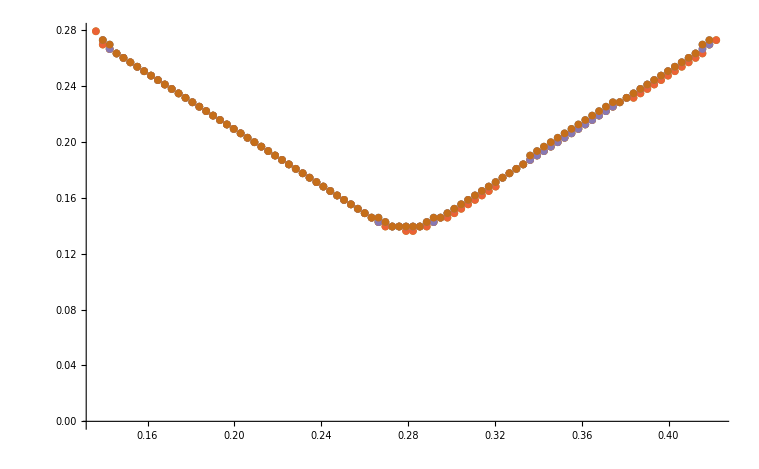

```mathematica
Show[ListPlot[ConOriFSRe1]]
```

```mathematica
Plot3D[{eng[kx,ky,2 Pi/c],0},{ky,0.45*a/a,0.663*a/a},{kx,0.2*a/a,0.35*a/a}]
```

InterpolatingFunction::dmval: Input value {0.200011,0.450015} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Calculate the ADMR
```

```mathematica
tdevs=800;
θdevs=8;
thetas =(*{80.,100.}*Pi/180*) Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}];
phis = {0.*Pi/180(*,15.*Pi/180,30.*Pi/180,45.*Pi/180*)};
param=Flatten[Table[{the,phi},{the,thetas},{phi,phis}],1]
hopping={{0.1}};
```

{{0.,0.},{0.218166,0.},{0.436332,0.},{0.654498,0.},{0.872665,0.},{1.09083,0.},{1.309,0.},{1.52716,0.},{1.74533,0.}}

```mathematica
Brange=(*Range[41,45,1]*){45};
tnum =8;

numbTimes=1;
numGrid01=Length[start01];


(*velocityz01=velocity01[[3]];*)
 cond01= Table[Table[{0,0,0},{Length[thetas]}],{Length[phis]}];

(*start01= Drop[Import["FS_kx_ky_kz.dat","Table"],1];
 *)
Bfield=45*1.6*10^-19 * 10^-12/(9.1*10^-31);
(*efun=Compile[{{kx,_Real},{ky,_Real},{kz,_Real}},inplanFermi[kx,ky]+ξz[kx,ky,kz]];*)
efun01[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];

(*eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];*)
h=10^-8;
velocity01=(9.1*10^-31)10^-20/(10^-12)*1/ℏ*1/h({efun01[kx+h,ky,kz]-efun01[kx,ky,kz],efun01[kx,ky+h,kz]-efun01[kx,ky,kz],efun01[kx,ky,kz+h]-efun01[kx,ky,kz]});
velZ[kx_,ky_,kz_]=velocity01[[3]];
Dx01=(efun01[kx+h,ky,kz]-efun01[kx,ky,kz])/h;
Dy01=(efun01[kx,ky+h,kz]-efun01[kx,ky,kz])/h;
Dz01=(efun01[kx,ky,kz+h]-efun01[kx,ky,kz])/h;
```

```mathematica
cond01=Table[{0,0,0},Length[param]]
AbsoluteTiming[

ParallelDo[
Module[{(*kx1,ky1,kz1,*)p1,gridIndex,B = {0,0,1},state01,state11,state21,solution01=Table[Null,{Length[start01]}],(*Dx01,Dy01,Dz01,*)τ=hopping[[numbTimes,1]],
τt=tnum*hopping[[numbTimes,1]],τs=tnum*hopping[[numbTimes,1]]/tdevs,times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs],V01,Exps,taus,tauSum,result},


(*times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs];
solution01=Table[Null,{Length[start01]}];*)
B = {Bfield*Sin[param[[index,1]]]Cos[param[[index,2]]],Bfield*Sin[param[[index,1]]]Sin[param[[index,2]]],Bfield*Cos[param[[index,1]]]};

cond01[[index]]={param[[index,2]]*180./Pi,param[[index,1]]*180./Pi,0};


state01=First@NDSolve`ProcessEquations[{(11538.5)kx'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[1]],(11538.5)ky'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[2]],(11538.5)kz'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[3]],kx[0] ==  start01[[1,1]],ky[0] ==  start01[[1,2]],kz[0] ==  start01[[1,3]]},{kx,ky,kz},tvar];

NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
 solution01[[1]]=NDSolve`ProcessSolutions[state01];

For[p1=2,p1≤ Length[start01](*numGrid01*),p1++,
 state01=First@NDSolve`Reinitialize[state01,{kx[0] ==  start01[[p1,1]],ky[0] ==  start01[[p1,2]],kz[0] ==  start01[[p1,3]]}];
NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
solution01[[p1]]=NDSolve`ProcessSolutions[state01];
];
(*state01=First@NDSolve`ProcessEquations[{(11538.5)kx1'[tvar] == -(1)Cross[velocity01/.kx->kx1[tvar]/.ky->ky1[tvar]/.kz->kz1[tvar],B][[1]],(11538.5)ky1'[tvar] == -(1)Cross[velocity01/.kx->kx1[tvar]/.ky->ky1[tvar]/.kz->kz1[tvar],B][[2]],(11538.5)kz1'[tvar] == -(1)Cross[velocity01/.kx->kx1[tvar]/.ky->ky1[tvar]/.kz->kz1[tvar],B][[3]],kx1[0] ==  start01[[1,1]],ky1[0] ==  start01[[1,2]],kz1[0] ==  start01[[1,3]]},{kx1,ky1,kz1},tvar];

NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
 solution01[[1]]=NDSolve`ProcessSolutions[state01];

For[p1=2,p1≤ Length[start01](*numGrid01*),p1++,
 state01=First@NDSolve`Reinitialize[state01,{kx1[0] ==  start01[[p1,1]],ky1[0] ==  start01[[p1,2]],kz1[0] ==  start01[[p1,3]]}];
NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
solution01[[p1]]=NDSolve`ProcessSolutions[state01];
];
*)
Print[index];

V01=Table[velZ[solution01[[i,1,2]][#],solution01[[i,2,2]][#],solution01[[i,3,2]][#]]&/@times,{i,1,Length[start01]}];
Exps=Exp[-(times)/hopping[[numbTimes,1]]]*τs*10^-12;
cond01[[index,3]] = cond01[[index,3]]+Total[Table[((1/Sqrt[(Dx01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2 +(Dy01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2+(Dz01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2])*
circ01[[i]]*4*Pi/c/cdev*(velocity01[[3]]/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz
->solution01[[i,3,2]][0] )*
(Total[V01[[i]]*Exps])),{i,1,numGrid01,1}]];
str01=StringJoin[dir,"\\Calculations\\cdw_param",ToString[index],".dat"];
Export[str01,{cond01[[index]]}];
Remove[state01,state11,state21,solution01,times,V01,Exps,taus,tauSum,result];
ClearSystemCache[];]
,{index,Length[param]}]];
str01=Table[StringJoin[dir,"\\Calculations\\cdw_param",ToString[index],".dat"],{index,1,Length[param]}];
cond01 =Table[Import[#]&/@str01[[i]],{i,Length[str01]}];
cond01exp=Flatten[Import[#]&/@Flatten[str01,1],1];
Export[StringJoin[dir,"\\cdw_elect_tau_0p054_n.dat"],cond01exp,"Table"];
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

5

1

4

3

8

7

6

9

2

```mathematica
cond01dat=SortBy[Import[StringJoin[dir,"\\cdw_elect_tau_0p054_n.dat"],"Table"],First];
conphi = DeleteDuplicates[cond01dat[[All,1]]]
coplot = Table[Select[cond01dat,#[[1]]==conphi[[i]]&][[All,{2,3}]],{i,1,Length[conphi]}]
conInt = Interpolation[#]&/@coplot;
confinal =Table[ Table[{th,conInt[[i]][0]/conInt[[i]][th]},{th,0,100,2}],{i,1,Length[conInt]}];
```

{0.}

{{{0.,1.03775×10^-18},{12.5,1.02923×10^-18},{25.,1.00317×10^-18},{37.5,9.59189×10^-19},{50.,9.02633×10^-19},{62.5,8.55821×10^-19},{75.,8.44439×10^-19},{87.5,8.24417×10^-19},{100.,8.416×10^-19}}}

```mathematica
cond02dat=SortBy[Import[StringJoin[dir,"\\cdw_hole23_tau_0p08.dat"],"Table"],First]
conphi2 = DeleteDuplicates[cond02dat[[All,1]]]
coplot2= Table[Select[cond02dat,#[[1]]==conphi2[[i]]&][[All,{2,3}]],{i,1,Length[conphi2]}];
conInt2 = Interpolation[#]&/@coplot2;
confinal2=Table[ Table[{th,conInt2[[i]][0]/conInt2[[i]][th]},{th,0,100,2}],{i,1,Length[conInt2]}];
```

{{0.,0.,1.85769×10^-17},{0.,6.66667,1.85636×10^-17},{0.,13.3333,1.85231×10^-17},{0.,20.,1.8453×10^-17},{0.,26.6667,1.83492×10^-17},{0.,33.3333,1.82061×10^-17},{0.,40.,1.80161×10^-17},{0.,46.6667,1.77704×10^-17},{0.,53.3333,1.74608×10^-17},{0.,60.,1.70868×10^-17},{0.,66.6667,1.66701×10^-17},{0.,73.3333,1.62593×10^-17},{0.,80.,1.58866×10^-17},{0.,86.6667,1.56146×10^-17},{0.,93.3333,1.56143×10^-17},{0.,100.,1.58864×10^-17},{15.,0.,1.85769×10^-17},{15.,6.66667,1.85636×10^-17},{15.,13.3333,1.85231×10^-17},{15.,20.,1.8453×10^-17},{15.,26.6667,1.83491×10^-17},{15.,33.3333,1.82058×10^-17},{15.,40.,1.80155×10^-17},{15.,46.6667,1.77691×10^-17},{15.,53.3333,1.74586×10^-17},{15.,60.,1.70835×10^-17},{15.,66.6667,1.66677×10^-17},{15.,73.3333,1.62686×10^-17},{15.,80.,1.59361×10^-17},{15.,86.6667,1.5718×10^-17},{15.,93.3333,1.57171×10^-17},{15.,100.,1.59371×10^-17},{30.,0.,1.85769×10^-17},{30.,6.66667,1.85636×10^-17},{30.,13.3333,1.85231×10^-17},{30.,20.,1.84529×10^-17},{30.,26.6667,1.83489×10^-17},{30.,33.3333,1.82053×10^-17},{30.,40.,1.80144×10^-17},{30.,46.6667,1.77669×10^-17},{30.,53.3333,1.74546×10^-17},{30.,60.,1.70778×10^-17},{30.,66.6667,1.66647×10^-17},{30.,73.3333,1.62899×10^-17},{30.,80.,1.60355×10^-17},{30.,86.6667,1.59233×10^-17},{30.,93.3333,1.59225×10^-17},{30.,100.,1.60368×10^-17},{45.,0.,1.85769×10^-17},{45.,6.66667,1.85636×10^-17},{45.,13.3333,1.85231×10^-17},{45.,20.,1.84529×10^-17},{45.,26.6667,1.83488×10^-17},{45.,33.3333,1.82051×10^-17},{45.,40.,1.80138×10^-17},{45.,46.6667,1.77659×10^-17},{45.,53.3333,1.74528×10^-17},{45.,60.,1.70754×10^-17},{45.,66.6667,1.66641×10^-17},{45.,73.3333,1.63019×10^-17},{45.,80.,1.60856×10^-17},{45.,86.6667,1.60252×10^-17},{45.,93.3333,1.60251×10^-17},{45.,100.,1.60856×10^-17}}

{0.,15.,30.,45.}

```mathematica
cond03dat=SortBy[Import[StringJoin[dir,"\\cdw_hole1_tau_0p08.dat"],"Table"],First];
conphi3= DeleteDuplicates[cond03dat[[All,1]]]
coplot3= Table[Select[cond03dat,#[[1]]==conphi3[[i]]&][[All,{2,3}]],{i,1,Length[conphi3]}]
conInt3= Interpolation[#]&/@coplot3;
confinal3 =Table[ Table[{th,conInt3[[i]][0]/conInt3[[i]][th]},{th,0,100,2}],{i,1,Length[conInt3]}];
```

{0.,15.,30.,45.}

{{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.41971×10^-18},{26.6667,2.41347×10^-18},{33.3333,2.4049×10^-18},{40.,2.39351×10^-18},{46.6667,2.37863×10^-18},{53.3333,2.35952×10^-18},{60.,2.33567×10^-18},{66.6667,2.30789×10^-18},{73.3333,2.27808×10^-18},{80.,2.24604×10^-18},{86.6667,2.21909×10^-18},{93.3333,2.21856×10^-18},{100.,2.24476×10^-18}},{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.41971×10^-18},{26.6667,2.41346×10^-18},{33.3333,2.40486×10^-18},{40.,2.39343×10^-18},{46.6667,2.37848×10^-18},{53.3333,2.35925×10^-18},{60.,2.33525×10^-18},{66.6667,2.30753×10^-18},{73.3333,2.27894×10^-18},{80.,2.25118×10^-18},{86.6667,2.2306×10^-18},{93.3333,2.23052×10^-18},{100.,2.25035×10^-18}},{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.4197×10^-18},{26.6667,2.41344×10^-18},{33.3333,2.4048×10^-18},{40.,2.39328×10^-18},{46.6667,2.37818×10^-18},{53.3333,2.35869×10^-18},{60.,2.3344×10^-18},{66.6667,2.30681×10^-18},{73.3333,2.28072×10^-18},{80.,2.26177×10^-18},{86.6667,2.25364×10^-18},{93.3333,2.25363×10^-18},{100.,2.26093×10^-18}},{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.4197×10^-18},{26.6667,2.41343×10^-18},{33.3333,2.40477×10^-18},{40.,2.39321×10^-18},{46.6667,2.37802×10^-18},{53.3333,2.35841×10^-18},{60.,2.33396×10^-18},{66.6667,2.30645×10^-18},{73.3333,2.28165×10^-18},{80.,2.26721×10^-18},{86.6667,2.26519×10^-18},{93.3333,2.26474×10^-18},{100.,2.26592×10^-18}}}

```mathematica
plotall = Table[ Table[{th,(conInt[[i]][0])},{th,0,100,2}],{i,1,Length[conInt]}];
```

```mathematica
confinal
```

{{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00077},{10,1.0012},{12,1.00171},{14,1.0023},{16,1.00296},{18,1.00368},{20,1.00445},{22,1.00527},{24,1.00611},{26,1.00696},{28,1.00781},{30,1.00864},{32,1.00941},{34,1.01012},{36,1.01073},{38,1.01122},{40,1.01157},{42,1.01173},{44,1.0117},{46,1.01143},{48,1.01089},{50,1.01007},{52,1.00896},{54,1.00752},{56,1.00573},{58,1.00366},{60,1.0013},{62,0.998626},{64,0.995753},{66,0.992741},{68,0.98959},{70,0.986415},{72,0.983347},{74,0.98051},{76,0.978008},{78,0.975851},{80,0.974093},{82,0.973009},{84,0.972305},{86,0.971911},{88,0.971684},{90,0.971631},{92,0.97178},{94,0.972123},{96,0.972652},{98,0.97336},{100,0.974238}},{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00077},{10,1.0012},{12,1.00171},{14,1.0023},{16,1.00296},{18,1.00368},{20,1.00445},{22,1.00526},{24,1.0061},{26,1.00695},{28,1.00779},{30,1.0086},{32,1.00936},{34,1.01005},{36,1.01064},{38,1.0111},{40,1.01141},{42,1.01153},{44,1.01143},{46,1.01109},{48,1.01047},{50,1.00953},{52,1.00829},{54,1.00669},{56,1.00471},{58,1.00241},{60,0.999807},{62,0.99684},{64,0.993654},{66,0.990312},{68,0.986823},{70,0.983304},{72,0.979887},{74,0.976696},{76,0.97384},{78,0.971324},{80,0.969203},{82,0.967688},{84,0.966587},{86,0.965868},{88,0.965479},{90,0.965408},{92,0.965648},{94,0.966181},{96,0.966993},{98,0.968068},{100,0.969392}},{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00078},{10,1.0012},{12,1.00171},{14,1.00229},{16,1.00295},{18,1.00367},{20,1.00444},{22,1.00525},{24,1.00608},{26,1.00691},{28,1.00773},{30,1.00853},{32,1.00926},{34,1.0099},{36,1.01045},{38,1.01085},{40,1.01108},{42,1.01111},{44,1.01089},{46,1.0104},{48,1.00959},{50,1.00844},{52,1.00693},{54,1.00501},{56,1.00265},{58,0.99991},{60,0.996813},{62,0.993276},{64,0.989475},{66,0.985484},{68,0.98133},{70,0.977132},{72,0.973023},{74,0.969131},{76,0.965565},{78,0.962336},{80,0.959499},{82,0.957158},{84,0.955295},{86,0.953941},{88,0.953186},{90,0.953001},{92,0.95334},{94,0.954188},{96,0.955535},{98,0.957368},{100,0.95968}},{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00077},{10,1.0012},{12,1.00171},{14,1.00229},{16,1.00295},{18,1.00367},{20,1.00443},{22,1.00524},{24,1.00606},{26,1.00689},{28,1.0077},{30,1.00849},{32,1.0092},{34,1.00983},{36,1.01035},{38,1.01072},{40,1.01091},{42,1.01089},{44,1.01062},{46,1.01005},{48,1.00915},{50,1.00789},{52,1.00624},{54,1.00416},{56,1.00161},{58,0.998659},{60,0.995318},{62,0.991499},{64,0.987395},{66,0.983085},{68,0.978603},{70,0.97407},{72,0.96962},{74,0.96538},{76,0.961461},{78,0.957876},{80,0.954684},{82,0.951948},{84,0.94972},{86,0.948057},{88,0.947098},{90,0.946818},{92,0.947167},{94,0.948142},{96,0.94974},{98,0.951963},{100,0.954813}}}

```mathematica
{ListPlot[plotall],ListPlot[confinal]}
```

```mathematica
{,}
```

```mathematica
cond01
```

{{{0.,80.,2.89715×10^-18},{0.,100.,2.89243×10^-18}}}

```mathematica
{{{0.,80.00000000000001,3.4254358325374527*^-19},{0.,100.,3.424002142807138*^-19}}}+{{{0.,80.00000000000001,2.554606501177453*^-18},{0.,100.,2.5500345755107177*^-18}}}
```

{{{0.,160.,2.89715×10^-18},{0.,200.,2.89243×10^-18}}}

```mathematica
cond01
```

{{{15.,0.,4.28324×10^-34},{15.,50.,1.3595×10^-32},{15.,100.,1.27931×10^-33}}}

```mathematica
Length[cond01]
```

1

```mathematica
Dx01=Evaluate[D[efun01[kx,ky,kz],kx]];
```

```mathematica
Dx01/.kx->0/.ky->0/.kz->0
```

0.83819

```mathematica
Dx01[0,0,0]
```

efun01^(1,0,0)[kx,ky,kz][0,0,0]

```mathematica
phis
```

{0.}

```mathematica
datanamE =StringJoin[dir,"\\Calculations\\full_test_500",ToString[#],".dat"]&/@{1};
conductivityE=Import[#]&/@datanamE;









contabE=Table[Table[Select[conductivityE[[j]],#1[[1]]==phis[[i]]*180/Pi&],{i,1,Length[phis]}],{j,1,Length[conductivityE]}];
con01TestE=Table[Table[Table[{contabE[[k,j,i,2]],contabE[[k,j,i,3]]},{i,1,Length[contabE[[k,j]]]}],{j,1,Length[contabE[[k]]]}],{k,1,Length[contabE]}];
res01E=Table[Table[Table[{con01TestE[[k,i,j,1]],(1/con01TestE[[k,i,j,2]])/(0+1/con01TestE[[k,i,1,2]])},{j,1,Length[con01TestE[[k,i]]]}],{i,1,Length[con01TestE[[k]]]}],{k,1,Length[con01TestE]}];
```

```mathematica
contabE
```

{{{}}}

```mathematica
ListPlot[Table[Table[{cond01[[j,i,2]],cond01[[j,1,3]]/cond01[[j,i,3]]},{i,1,Length[cond01[[j]]]}],{j,1,Length[cond01],1}],PlotRange->{All,All}]
```

```mathematica
plotDatint=Table[Interpolation[Table[{cond01[[j,i,2]],cond01[[j,1,3]]/cond01[[j,i,3]]},{i,1,Length[cond01[[1]]]}]],{j,1,Length[phis]}];
plotDat=Table[Table[{cond01[[j,i,2]],cond01[[j,1,3]]/cond01[[j,i,3]]},{i,1,Length[cond01[[1]]]}],{j,1,Length[phis]}];
plotintdat = Table[Table[{x,plotDatint[[j]][x]},{x,0,100,5}],{j,1,Length[phis]}];

Show[Plot[{plotDatint[[1]][x],plotDatint[[2]][x],plotDatint[[3]][x],plotDatint[[4]][x]},{x,0,100}],ListPlot[plotDat]]
```

```mathematica
ListLinePlot[plotDat,PlotRange->{All,All},PlotStyle->({Blue,Red,Green,Orange}),Frame->True,FrameLabel->{{ Text[Style["R(θ)/R(0)",FontSize->24,FontFamily->"Helvetica"]],None},{Text[Style["θ(deg)",FontSize->20,FontFamily->"Helvetica"]],None}},FrameStyle->Directive[Black,Thickness[.001]],
FrameTicksStyle->Directive[Black,20,FontFamily->"Helvetica"],ImageSize->500,PlotRangePadding->None,PlotLegends->Placed[LineLegend[Directive[#,Thickness[.008]]&/@({Blue,Red,Green,Orange}),Text[Style[#,FontSize->12,FontFamily->"Franklin Gothic"]]&/@{"phi=0","phi=15","phi=30","phi=45"},LegendFunction->"Frame",LegendMarkerSize->12,LegendLayout->{"Column",1}],{0.15,0.5}]]
```

```mathematica
checkpoint =StringJoin["Calculations//exp_angles0_phi_0_grixInd_",ToString[#],".dat"]&/@Range[1,(*cdevs*)Length[start01]-1,1];
testdat = Import[#,"Table"]&/@checkpoint;
```

```mathematica
Transpose[Drop[testdat[[1]],-1]]
```

{{0.161434,0.266388,-0.237999,0.},{0.168781,0.258142,-0.237999,0.0064},{0.177027,0.249759,-0.237999,0.0128},{0.185659,0.241247,-0.237999,0.0192},{0.19446,0.23262,-0.237999,0.0256},{0.203323,0.223894,-0.237999,0.032},{0.212186,0.215091,-0.237999,0.0384},{0.221009,0.206237,-0.237999,0.0448},{0.229763,0.197369,-0.237999,0.0512},{0.238424,0.188538,-0.237999,0.0576},{0.246976,0.179834,-0.237999,0.064},{0.255402,0.171425,-0.237999,0.0704},{0.263694,0.163692,-0.237999,0.0768},{0.27185,0.157599,-0.237999,0.0832},{0.279908,0.155262,-0.237999,0.0896},{0.287973,0.158182,-0.237999,0.096},{0.296145,0.164557,-0.237999,0.1024},{0.304453,0.172406,-0.237999,0.1088},{0.312895,0.180863,-0.237999,0.1152},{0.32146,0.189589,-0.237999,0.1216},{0.330134,0.198428,-0.237999,0.128},{0.338897,0.207297,-0.237999,0.1344},{0.347727,0.216145,-0.237999,0.1408},{0.356592,0.22494,-0.237999,0.1472},{0.365452,0.233655,-0.237999,0.1536},{0.37424,0.242269,-0.237999,0.16},{0.382841,0.250767,-0.237999,0.1664},{0.391015,0.259134,-0.237999,0.1728},{0.398194,0.267363,-0.237999,0.1792},{0.40293,0.275467,-0.237999,0.1856},{0.402889,0.283512,-0.237999,0.192},{0.398096,0.291617,-0.237999,0.1984},{0.390895,0.299849,-0.237999,0.2048},{0.382711,0.308218,-0.237999,0.2112},{0.374105,0.316718,-0.237999,0.2176},{0.365315,0.325334,-0.237999,0.224},{0.356455,0.33405,-0.237999,0.2304},{0.34759,0.342846,-0.237999,0.2368},{0.338761,0.351696,-0.237999,0.2432},{0.33,0.360565,-0.237999,0.2496},{0.321327,0.369403,-0.237999,0.256},{0.312764,0.378127,-0.237999,0.2624},{0.304323,0.386578,-0.237999,0.2688},{0.296017,0.394412,-0.237999,0.2752},{0.287848,0.400753,-0.237999,0.2816},{0.279784,0.403599,-0.237999,0.288},{0.271725,0.401187,-0.237999,0.2944},{0.263566,0.395055,-0.237999,0.3008},{0.255272,0.387306,-0.237999,0.3072},{0.246844,0.378891,-0.237999,0.3136},{0.23829,0.370184,-0.237999,0.32},{0.229627,0.361352,-0.237999,0.3264},{0.220872,0.352483,-0.237999,0.3328},{0.212048,0.343631,-0.237999,0.3392},{0.203185,0.334829,-0.237999,0.3456},{0.194322,0.326104,-0.237999,0.352},{0.185522,0.317479,-0.237999,0.3584},{0.176894,0.308969,-0.237999,0.3648},{0.168656,0.300587,-0.237999,0.3712},{0.161328,0.292344,-0.237999,0.3776},{0.156228,0.284228,-0.237999,0.384},{0.155699,0.276183,-0.237999,0.3904},{0.160103,0.268088,-0.237999,0.3968},{0.167142,0.259871,-0.237999,0.4032},{0.175258,0.251516,-0.237999,0.4096},{0.183833,0.24303,-0.237999,0.416},{0.19261,0.234425,-0.237999,0.4224},{0.201467,0.225718,-0.237999,0.4288},{0.210334,0.21693,-0.237999,0.4352},{0.219168,0.208085,-0.237999,0.4416},{0.227938,0.199216,-0.237999,0.448},{0.236621,0.190372,-0.237999,0.4544},{0.245197,0.181631,-0.237999,0.4608},{0.25365,0.17314,-0.237999,0.4672},{0.26197,0.165213,-0.237999,0.4736},{0.270154,0.158642,-0.237999,0.48},{0.278225,0.155305,-0.237999,0.4864},{0.286278,0.157187,-0.237999,0.4928},{0.294423,0.163049,-0.237999,0.4992},{0.302702,0.170689,-0.237999,0.5056},{0.311117,0.179058,-0.237999,0.512},{0.319658,0.187744,-0.237999,0.5184},{0.328311,0.196567,-0.237999,0.5248},{0.337057,0.205435,-0.237999,0.5312},{0.345875,0.214292,-0.237999,0.5376},{0.354735,0.2231,-0.237999,0.544},{0.363601,0.231834,-0.237999,0.5504},{0.372411,0.240471,-0.237999,0.5568},{0.381065,0.248994,-0.237999,0.5632},{0.389361,0.257389,-0.237999,0.5696},{0.396827,0.265647,-0.237999,0.576},{0.40226,0.273774,-0.237999,0.5824},{0.403358,0.281822,-0.237999,0.5888},{0.399378,0.289907,-0.237999,0.5952},{0.392522,0.298111,-0.237999,0.6016},{0.384479,0.306451,-0.237999,0.608},{0.375937,0.314924,-0.237999,0.6144},{0.367175,0.323517,-0.237999,0.6208},{0.358323,0.332214,-0.237999,0.6272},{0.349455,0.340995,-0.237999,0.6336},{0.340615,0.349836,-0.237999,0.64}}

```mathematica
Show[ListPointPlot3D[Transpose[Drop[testdat[[#]],-2]]&/@Range[1,Length[start01]-1,1]],ListPointPlot3D[start01]]
```

```mathematica
ListPlot[Table[Table[{i,eng[timeCoor[[j,i,1]],timeCoor[[j,i,2]],timeCoor[[j,i,2]],μ]},{i,1,Length[timeCoor[[1]]]}],{j,1,Length[timeCoor]}]]
```

```mathematica
ty
```

17582.4

```mathematica
h = 10^-6;
eng[kx_,ky_,kz_,mu_]:=BDWbands[kx, ky,mu][[4]]+ξz[kx,ky,kz];
GradN = Table[{start[[i,{1,2}]],Sign[(eng[start[[i,1]], start[[i,2]],start[[i,3]]+h,μ]-eng[start[[i,1]], start[[i,2]],start[[i,3]],μ])]*{(eng[start[[i,1]]+h, start[[i,2]],start[[i,3]],μ]-eng[start[[i,1]], start[[i,2]],start[[i,3]],μ])/h,(eng[start[[i,1]], start[[i,2]]+h,start[[i,3]],μ]-eng[start[[i,1]], start[[i,2]],start[[i,3]],μ])/h}},{i,1,Length[start]}];
GradN3d = Table[{(eng[start[[i,1]]+h, start[[i,2]],start[[i,3]],μ]-eng[start[[i,1]], start[[i,2]],start[[i,3]],μ])/h,(eng[start[[i,1]], start[[i,2]]+h,start[[i,3]],μ]-eng[start[[i,1]], start[[i,2]],start[[i,3]],μ])/h,(eng[start[[i,1]], start[[i,2]],start[[i,3]],μ]-eng[start[[i,1]], start[[i,2]],start[[i,3]]+h,μ])/h},{i,1,Length[start]}];
```

```mathematica
Bfield=45*1.6*10^-19 * 10^-12/(9.1*10^-31);
B = {Bfield*Sin[thetas[[1]]]Cos[phis[[1]]],Bfield*Sin[thetas[[1]]]Sin[phis[[1]]],Bfield*Cos[thetas[[1]]]};
```

```mathematica
Show[DensityPlot[A4[kx,ky,μ,0],{ky,0.55/a,1.55/a},{kx,0.55/a,1.55/a},PlotPoints->200,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor],ListVectorPlot[GradN,VectorPoints->All]]
```

Zoom on the electron pocket (small portion of FS), and corresponding eigenvalue

```mathematica
ContourPlot[BDWbands[kx,ky,-0.8][[4]]==0,{kx,0.55,1.55},{ky,0.55,1.55}]
```

$Aborted

```mathematica
BDWbands[kx,ky,-0.8][[4]]
```

$Aborted

```mathematica
GraphicsRow[{
DensityPlot[A4[kx,ky,μ,0],{ky,0.55/a,1.55/a},{kx,0.55/a,1.55/a},PlotPoints->100,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor],
Plot3D[{BDWbands[kx,ky,μ][[4]],0},{kx,0.55/a,1.55/a},{ky,0.55/a,1.55/a},MaxRecursion->4,BoxRatios->{1, 1, 1},PlotStyle->{{Opacity[1]},{Opacity[0.3]}}]
},ImageSize->Full]
```

```mathematica
Clear[BDW2d,ξ,ξz,tyQ,txQ,tsxQ,tsyQ,Q,μ]
```

```mathematica
(*ξ[kx_,ky_,mu_]:=E;*)
ξz[kx_,ky_,kz_]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];
tyQ[kx_,ky_]:=Δ;
txQ[kx_,ky_]:=Δ;

BDW2d[kx_,ky_,mu_]=({{ξ[kx,ky,mu], tyQ[kx,ky+Q/2], tyQ[kx,ky-Q/2], txQ[kx+Q/2,ky], 0, 0, txQ[kx-Q/2,ky], 0, 0}, {tyQ[kx,ky+Q/2], ξ[kx,ky+Q,mu], tyQ[kx,ky], 0, txQ[kx+Q/2,ky+Q], 0, 0, txQ[kx-Q/2,ky+Q], 0}, {tyQ[kx,ky-Q/2], tyQ[kx,ky], ξ[kx,ky-Q,mu], 0, 0, txQ[kx+Q/2,ky-Q], 0, 0, txQ[kx-Q/2,ky-Q]}, {txQ[kx+Q/2,ky], 0, 0, ξ[kx+Q,ky,mu], tyQ[kx+Q,ky+Q/2], tyQ[kx+Q,ky-Q/2], txQ[kx,ky], 0, 0}, {0, txQ[kx+Q/2,ky+Q], 0, tyQ[kx+Q,ky+Q/2], ξ[kx+Q,ky+Q,mu], tyQ[kx+Q,ky], 0, txQ[kx,ky+Q], 0}, {0, 0, txQ[kx+Q/2,ky-Q], tyQ[kx+Q,ky-Q/2], tyQ[kx+Q,ky], ξ[kx+Q,ky-Q,mu], 0, 0, txQ[kx,ky-Q]}, {txQ[kx-Q/2,ky], 0, 0, txQ[kx,ky], 0, 0, ξ[kx-Q,ky,mu], tyQ[kx-Q,ky+Q/2], tyQ[kx-Q,ky-Q/2]}, {0, txQ[kx-Q/2,ky+Q], 0, 0, txQ[kx,ky+Q], 0, tyQ[kx-Q,ky+Q/2], ξ[kx-Q,ky+Q,mu], tyQ[kx-Q,ky]}, {0, 0, txQ[kx-Q/2,ky-Q], 0, 0, txQ[kx,ky-Q], tyQ[kx-Q,ky-Q/2], tyQ[kx-Q,ky], ξ[kx-Q,ky-Q,mu]}})
```

{{ξ[kx,ky,mu],Δ,Δ,Δ,0,0,Δ,0,0},{Δ,ξ[kx,ky+Q,mu],Δ,0,Δ,0,0,Δ,0},{Δ,Δ,ξ[kx,ky-Q,mu],0,0,Δ,0,0,Δ},{Δ,0,0,ξ[kx+Q,ky,mu],Δ,Δ,Δ,0,0},{0,Δ,0,Δ,ξ[kx+Q,ky+Q,mu],Δ,0,Δ,0},{0,0,Δ,Δ,Δ,ξ[kx+Q,ky-Q,mu],0,0,Δ},{Δ,0,0,Δ,0,0,ξ[kx-Q,ky,mu],Δ,Δ},{0,Δ,0,0,Δ,0,Δ,ξ[kx-Q,ky+Q,mu],Δ},{0,0,Δ,0,0,Δ,Δ,Δ,ξ[kx-Q,ky-Q,mu]}}

```mathematica
MatrixForm[BDW2d[kx,ky,μ]]
```

(ξ[kx,ky,μ] | Δ | Δ | Δ | 0 | 0 | Δ | 0 | 0
Δ | ξ[kx,ky+Q,μ] | Δ | 0 | Δ | 0 | 0 | Δ | 0
Δ | Δ | ξ[kx,ky-Q,μ] | 0 | 0 | Δ | 0 | 0 | Δ
Δ | 0 | 0 | ξ[kx+Q,ky,μ] | Δ | Δ | Δ | 0 | 0
0 | Δ | 0 | Δ | ξ[kx+Q,ky+Q,μ] | Δ | 0 | Δ | 0
0 | 0 | Δ | Δ | Δ | ξ[kx+Q,ky-Q,μ] | 0 | 0 | Δ
Δ | 0 | 0 | Δ | 0 | 0 | ξ[kx-Q,ky,μ] | Δ | Δ
0 | Δ | 0 | 0 | Δ | 0 | Δ | ξ[kx-Q,ky+Q,μ] | Δ
0 | 0 | Δ | 0 | 0 | Δ | Δ | Δ | ξ[kx-Q,ky-Q,μ])

```mathematica
ξ[kx_,ky_,mu_]:=-2t(Cos[kx a]+Cos[ky b])-2tp(Cos[kx a+ky b]+Cos[kx a- ky b])-2tpp(Cos[2kx a]+Cos[2ky b])+mu;
ξz[kx_,ky_,kz_]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];
```

```mathematica
tp=-0.16*t;
tpp=0.07*t;
tz=0.07*t;
μ = 0.8*t;
ξ[kx_,ky_,mu_]:=-2t(Cos[kx a]+Cos[ky b])-2tp(Cos[kx a+ky b]+Cos[kx a- ky b])-2tpp(Cos[2kx a]+Cos[2ky b])+mu;
ξz[kx_,ky_,kz_]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];

AA=0.1*t;
Q=2π/3/a;
(*here it could be functions of kx and ky like for dwave density waves*)
tyQ[kx_,ky_]:=AA;
txQ[kx_,ky_]:=AA;

BDW2d[kx_,ky_,mu_]=({{ξ[kx,ky,mu], tyQ[kx,ky+Q/2], tyQ[kx,ky-Q/2], txQ[kx+Q/2,ky], 0, 0, txQ[kx-Q/2,ky], 0, 0}, {tyQ[kx,ky+Q/2], ξ[kx,ky+Q,mu], tyQ[kx,ky], 0, txQ[kx+Q/2,ky+Q], 0, 0, txQ[kx-Q/2,ky+Q], 0}, {tyQ[kx,ky-Q/2], tyQ[kx,ky], ξ[kx,ky-Q,mu], 0, 0, txQ[kx+Q/2,ky-Q], 0, 0, txQ[kx-Q/2,ky-Q]}, {txQ[kx+Q/2,ky], 0, 0, ξ[kx+Q,ky,mu], tyQ[kx+Q,ky+Q/2], tyQ[kx+Q,ky-Q/2], txQ[kx,ky], 0, 0}, {0, txQ[kx+Q/2,ky+Q], 0, tyQ[kx+Q,ky+Q/2], ξ[kx+Q,ky+Q,mu], tyQ[kx+Q,ky], 0, txQ[kx,ky+Q], 0}, {0, 0, txQ[kx+Q/2,ky-Q], tyQ[kx+Q,ky-Q/2], tyQ[kx+Q,ky], ξ[kx+Q,ky-Q,mu], 0, 0, txQ[kx,ky-Q]}, {txQ[kx-Q/2,ky], 0, 0, txQ[kx,ky], 0, 0, ξ[kx-Q,ky,mu], tyQ[kx-Q,ky+Q/2], tyQ[kx-Q,ky-Q/2]}, {0, txQ[kx-Q/2,ky+Q], 0, 0, txQ[kx,ky+Q], 0, tyQ[kx-Q,ky+Q/2], ξ[kx-Q,ky+Q,mu], tyQ[kx-Q,ky]}, {0, 0, txQ[kx-Q/2,ky-Q], 0, 0, txQ[kx,ky-Q], tyQ[kx-Q,ky-Q/2], tyQ[kx-Q,ky], ξ[kx-Q,ky-Q,mu]}});
BDWbands[kx_,ky_,mu_?NumericQ]:=BDWbands[kx,ky,mu]=Sort[Eigenvalues[BDW2d[kx,ky,mu]]];
```

```mathematica
c=13.2;
a =5.3/Sqrt[2];
```

```mathematica
Plot[1/(BesselJ[0,(1/a)*(c/2)*Tan[thetas*Pi/180]]+1)^2,{thetas,0,100}]
```

```mathematica
ClearAll[V01]
```

```mathematica
thetas={80,100}*Pi/180.;
phis={0}*Pi/180;
```

```mathematica
angleIndex=1;
phiIndex=1;
tnum=8;
numbTimes=1;
hopping={{0.02}}
solution=Table[Table[Null,{Length[start01]}],{Length[thetas]}];
efun01[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=BDWbands[kx, ky,μ][[4]]+ξz[kx,ky,kz];
h=10^-10;
velocity01=(9.1*10^-31)10^-20/(10^-12)*1/ℏ*1/h({efun01[kx+h,ky,kz]-efun01[kx,ky,kz],efun01[kx,ky+h,kz]-efun01[kx,ky,kz],efun01[kx,ky,kz+h]-efun01[kx,ky,kz]});
velZ[kx_,ky_,kz_]=velocity01[[3]];
times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs];
τs=tnum*hopping[[numbTimes,1]]/tdevs
Dx01=(efun01[kx+h,ky,kz]-efun01[kx,ky,kz])/h;
Dy01=(efun01[kx,ky+h,kz]-efun01[kx,ky,kz])/h;
Dz01=(efun01[kx,ky,kz+h]-efun01[kx,ky,kz])/h;
```

{{0.02}}

0.0002

```mathematica
AbsoluteTiming[Do[

angleIndex=index;
B = {Bfield*Sin[thetas[[angleIndex]]]Cos[phis[[phiIndex]]],Bfield*Sin[thetas[[angleIndex]]]Sin[phis[[phiIndex]]],Bfield*Cos[thetas[[angleIndex]]]};
state01=First@NDSolve`ProcessEquations[{(11538.5)kx'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[1]],(11538.5)ky'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[2]],(11538.5)kz'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[3]],kx[0] ==  start01[[1,1]],ky[0] ==  start01[[1,2]],kz[0] ==  start01[[1,3]]},{kx,ky,kz},tvar];

NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)]; solution[[index,1]]=NDSolve`ProcessSolutions[state01];

For[p1=2,p1≤(* Length[start01]*)numGrid01,p1++, state01=First@NDSolve`Reinitialize[state01,(*{kx[0] ==  start01[[p1,1]],ky[0] ==  start01[[p1,2]],kz[0] ==  start01[[p1,3]]}*){kx[0] ==  start01[[p1,1]],ky[0] ==  start01[[p1,2]],kz[0] ==  start01[[p1,3]]}];NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum)]; solution[[index,p1]]=NDSolve`ProcessSolutions[state01];];
ClearAll[state01]
,{index,Length[thetas]}]]
```

{81.4696,Null}

```mathematica
AbsoluteTiming[V01=Table[Table[velZ[solution[[j,i,1,2]][#],solution[[j,i,2,2]][#],solution[[j,i,3,2]][#]]&/@times,{i,1,Length[start01]}],{j,{1,Length[solution]}}];]
```

{156.704,Null}

```mathematica
Exps=Exp[-(times)/hopping[[numbTimes,1]]]*τs*10^-12;
```

```mathematica
Table[((1/Sqrt[(Dx01/.kx->solution[[1,i,1,2]][0]/.ky->solution[[1,i,2,2]][0]/.kz->solution[[1,i,3,2]][0])^2 +(Dy01/.kx->solution[[1,i,1,2]][0]/.ky->solution[[1,i,2,2]][0]/.kz->solution[[1,i,3,2]][0])^2+(Dz01/.kx->solution[[1,i,1,2]][0]/.ky->solution[[1,i,2,2]][0]/.kz->solution[[1,i,3,2]][0])^2])*
circ01[[i]]*4*Pi/c/cdev*(velocity01[[3]]/.kx->solution[[1,i,1,2]][0]/.ky->solution[[1,i,2,2]][0]/.kz->solution[[1,i,3,2]][0] )*
(Total[V01[[1,i]]*Exps])),{i,1,Length[start01],1}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
velocity01[[3]]/.kx->solution[[1,1,1,2]][0]/.ky->solution[[1,1,2,2]][0]/.kz->solution[[1,1,3,2]][0]
```

0.

```mathematica
Total[V01[[1,1]]*Exps]
```

-6.3472×10^-14

```mathematica
AbsoluteTiming[
con01=Table[0,Length[solution]];
Do[

con01[[j]]=Total[Table[((1/Sqrt[(Dx01/.kx->solution[[j,i,1,2]][0]/.ky->solution[[j,i,2,2]][0]/.kz->solution[[j,i,3,2]][0])^2 +(Dy01/.kx->solution[[j,i,1,2]][0]/.ky->solution[[j,i,2,2]][0]/.kz->solution[[j,i,3,2]][0])^2+(Dz01/.kx->solution[[j,i,1,2]][0]/.ky->solution[[j,i,2,2]][0]/.kz->solution[[j,i,3,2]][0])^2])*
circ01[[i]]*4*Pi/c/cdev*(velocity01[[3]]/.kx->solution[[j,i,1,2]][0]/.ky->solution[[j,i,2,2]][0]/.kz
->solution[[j,i,3,2]][0] )*
(Total[V01[[j,i]]*Exps])),{i,1,Length[start01],1}]];,{j,1,Length[solution]}]]
```

{0.515388,Null}

```mathematica
con01
```

{3.42544×10^-19,3.424×10^-19}

```mathematica
trajphi=Table[Transpose[{solution[[i,#,1,2]][times],solution[[i,#,2,2]][times],solution[[i,#,3,2]][times]}]&/@Range[1,Length[start01],10],{i,1,Length[solution]}];
```

```mathematica
grid = Transpose[{solution[[1,1,1,2]][times],solution[[1,1,2,2]][times],solution[[1,1,3,2]][times]}];
```

```mathematica
ListPointPlot3D[trajphi[[1,1]]]
```

```mathematica
test =Table[efun01[solution[[1,1,1,2]][times[[i]]],solution[[1,1,2,2]][times[[i]]],solution[[1,1,3,2]][times[[i]]]],{i,1,Length[times]}]
```

```mathematica
solution[[1,1,3,2]][0]
```

-0.416499

```mathematica
times[[1]]
```

0.

```mathematica
test[[1]]
```

48.6252

```mathematica
ListPlot[test]
```

```mathematica
t=190*ty;
tp=-0.16*t;
tpp=0.07*t;
tz=0.035*t;
μ = 0.635*t;
ξ[kx_,ky_,mu_]:=-2t(Cos[kx a]+Cos[ky b])-2tp(Cos[kx a+ky b]+Cos[kx a- ky b])-2tpp(Cos[2kx a]+Cos[2ky b])+mu;
ξz[kx_,ky_,kz_]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];


Q=2π/3/a;
(*here it could be functions of kx and ky like for dwave density waves*)
B=0(*-0.07*t*);
AA=0.1*t;

(*here it could be functions of kx and ky like for dwave density waves*)
tyQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);
txQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b] );
tsyQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);
tsxQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);

BDW2d[kx_,ky_,mu_]=({{ξ[kx,ky,mu], -tyQ[kx,ky+Q/2], -tyQ[kx,ky-Q/2], -txQ[kx+Q/2,ky], 0, 0, -txQ[kx-Q/2,ky], 0, 0}, {-tyQ[kx,ky+Q/2], ξ[kx,ky+Q,mu], -tyQ[kx,ky-3/2Q], 0, -tsxQ[kx+Q/2,ky+Q], 0, 0, -tsxQ[kx-Q/2,ky+Q], 0}, {-tyQ[kx,ky-Q/2], -tyQ[kx,ky+3/2Q], ξ[kx,ky+2Q,mu], 0, 0, -tsxQ[kx+Q/2,ky-Q], 0, 0, -tsxQ[kx-Q/2,ky-Q]}, {-txQ[kx+Q/2,ky], 0, 0, ξ[kx+Q,ky,mu], -tsyQ[kx+Q,ky+Q/2], -tsyQ[kx+Q,ky-Q/2], -txQ[kx-3/2Q,ky], 0, 0}, {0, -tsxQ[kx+Q/2,ky+Q], 0, -tsyQ[kx+Q,ky+Q/2], ξ[kx+Q,ky+Q,mu], -tsyQ[kx+Q,ky-3/2Q], 0, -tsxQ[kx-3/2Q,ky+Q], 0}, {0, 0, -tsxQ[kx+Q/2,ky-Q], -tsyQ[kx+Q,ky-Q/2], -tsyQ[kx+Q,3/2Q+ky], ξ[kx+Q,ky+2Q,mu], 0, 0, -tsxQ[kx-3/2Q,ky-Q]}, {-txQ[kx-Q/2,ky], 0, 0, -txQ[kx+3/2Q,ky], 0, 0, ξ[kx+2Q,ky,mu], -tsyQ[kx-Q,ky+Q/2], -tsyQ[kx-Q,ky-Q/2]}, {0, -tsxQ[kx-Q/2,ky+Q], 0, 0, -tsxQ[kx+3/2Q,ky+Q], 0, -tsyQ[kx-Q,ky+Q/2], ξ[kx+2Q,ky+Q,mu], -tsyQ[kx-Q,ky-3/2Q]}, {0, 0, -tsxQ[kx-Q/2,ky-Q], 0, 0, -tsxQ[kx+3/2Q,ky-Q], -tsyQ[kx-Q,ky-Q/2], -tsyQ[kx-Q,ky+3/2Q], ξ[kx+2Q,ky+2Q,mu]}});
BDWbands[kx_,ky_,mu_?NumericQ]:=BDWbands[kx,ky,mu]=Sort[Eigenvalues[BDW2d[kx,ky,mu]]];
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=BDWbands[kx, ky,μ][[4]]+ξz[kx,ky,kz];
```

```mathematica
Plot3D[{eng[kx,ky,0],0},{kx,(1-1.5dist)/a,(1+1.5dist)/a},{ky,(1-1.5dist)/a,(1+1.5dist)/a},MaxRecursion->4,BoxRatios->{1, 1, 1},PlotStyle->{{Opacity[1]},{Opacity[0.3]}},PlotRange->{{(1.05-0.96dist)/a,(1.05+0.96dist)/a},{(1.05-dist)/a,(1.05+dist)/a},All}]
```

```mathematica
Plot3D[{eng[kx,ky,2*Pi/c],0},{kx,0.2*a/a,0.37*a/a},{ky,-1.16* 0.09*a/a,1.16* 0.09*a/a},MaxRecursion->4,BoxRatios->{1, 1, 1},PlotStyle->{{Opacity[1]},{Opacity[0.3]}},PlotRange->{{0.2*a/a,0.37*a/a},{-1.14* 0.09*a/a,1.14* 0.09*a/a},All}]
```

```mathematica
Plot3D[{eng[kx,ky,2*Pi/c],0},{kx,0.45*a/a,0.68*a/a},{ky,0.5/a,1.58/a},MaxRecursion->4,BoxRatios->{1, 1, 1},PlotStyle->{{Opacity[1]},{Opacity[0.3]}},PlotRange->{{0.45*a/a,0.665*a/a},{0.5/a,1.58/a},All}]
```

```mathematica
0.5/a
```

0.133416